```mathematica
(* setup differential equation *)
u'[t] == -α u[t];
u[0]==β;
(* alpha is normally distributed *)
μ = 10;
σ = 2;
α[z_]:=μ + σ z;
(* beta is deterministic *)
β = 5;
(* both alpha and beta need to be projected onto a basis of Hermite polynomials *)
γ[i_]:=∫_(-∞)^∞ HermiteH[i,z]^2 ⅇ^(-z^2)ⅆz;
a[i_]:=(∫_(-∞)^∞ α[z]HermiteH[i,z] ⅇ^(-z^2)ⅆz)/γ[i]
b[i_]:=(∫_(-∞)^∞ β HermiteH[i,z] ⅇ^(-z^2)ⅆz)/γ[i]
αN[n_,z_]:=∑_(i=0)^n a[i]HermiteH[i,z]
vN[n_,t_,z_]:=∑_(i=0)^n vhat[i,t]*HermiteH[i,z]
(* By substituting vN for u and αN for α into the differential equation the following arrives *)
n=1;
(*eq1=D[vN[n,t,z],t] ==-αN[n,z]vN[n,t,z];*)
(*D[vN[n,t,z],t] HermiteH[k,z] ⅇ^(-z^2)==-αN[n,z]vN[n,t,z]HermiteH[k,z] ⅇ^(-z^2);
eq2=∫_(-∞)^∞ D[vN[n,t,z],t] HermiteH[k,z] ⅇ^(-z^2)ⅆz==∫_(-∞)^∞ -αN[n,z]vN[n,t,z]HermiteH[k,z] ⅇ^(-z^2)ⅆz;
D[vhat[k,t],t]γ[k]==∫_(-∞)^∞ -αN[n,z]vN[n,t,z]HermiteH[k,z] ⅇ^(-z^2)ⅆz;
D[vhat[k,t],t]γ[k]==∫_(-∞)^∞ -∑_(i=0)^n a[i]HermiteH[i,z]∑_(i=0)^n vhat[i,t]*HermiteH[i,z]HermiteH[k,z] ⅇ^(-z^2)ⅆz;
D[vhat[k,t],t]γ[k]==-∑_(i=0)^n ∑_(j=0)^n a[i]vhat[j,t]∫_(-∞)^∞ HermiteH[i,z]*HermiteH[j,z]HermiteH[k,z] ⅇ^(-z^2)ⅆz;*)
e[i_,j_,k_]:=∫_(-∞)^∞ HermiteH[i,z]*HermiteH[j,z]HermiteH[k,z] ⅇ^(-z^2)ⅆz;
(*D[vhat[k,t],t]γ[k]==-∑_(i=0)^n ∑_(j=0)^n a[i]vhat[j,t]e[i,j,k];*)
```

```mathematica
n=1;
sol=DSolve[{
D[vhat[0,t],t]==-1/γ[0]-∑_(i=0)^n ∑_(j=0)^n a[i]vhat[j,t]e[i,j,0],
vhat[0,0]==b[0],
D[vhat[1,t],t]==-1/γ[1]-∑_(i=0)^n ∑_(j=0)^n a[i]vhat[j,t]e[i,j,1],
vhat[1,0]==b[1]},{vhat[0,t],vhat[1,t]},t];
v1[t_,z_]:=∑_(i=0)^n vhat[i,t]*HermiteH[i,z]/.sol;
```

```mathematica
Plot3D[v1[t,z],{t,0,.5},{z,5,15},PlotRange->All]
```

-Graphics3D-

```mathematica
Manipulate[Plot[v1[t,z],{t,-.1,.5}],{z,5,15}]
```

```mathematica
(* Mean solution *)
v1μ[t_]:=∫_(-∞)^∞ v1[t,z] ⅇ^(-z^2)ⅆz
(* standard deviation of solution *)
v1σ[t_]:=√(∫_(-∞)^∞ v1[t,z]^2 ⅇ^(-z^2)ⅆz -v1μ[t]^2)
```

```mathematica
v1μ[t]
```

{(ⅇ^(-(15+√29) √π t) (551-89 √29-1102 ⅇ^((15+√29) √π t)-980 (-29+5 √29) π+ⅇ^(2 √(29 π) t) (551+89 √29+980 (29+5 √29) π)))/(11368 √π)}

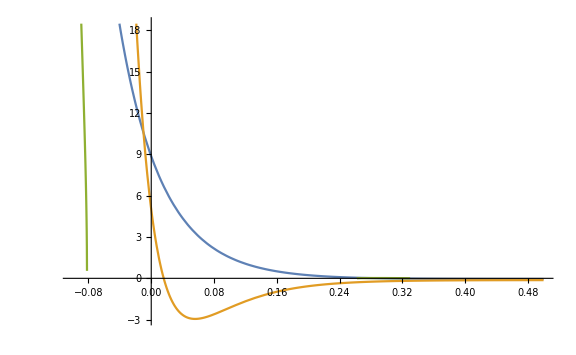

```mathematica
Plot[{v1μ[t],v1[t,10],v1σ[t]},{t,-.1,.5},ImageSize->Large]
```